```mathematica
With[{indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]]},
With[{SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2]},Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]]]
```

-Graphics-

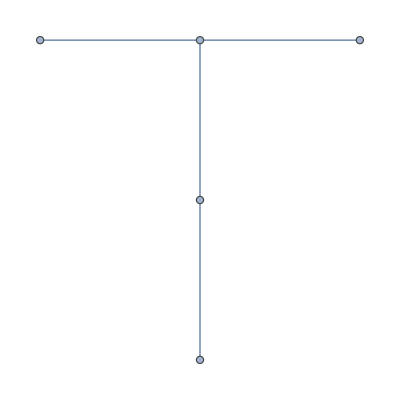

```mathematica
(* 1. creates a nearest neighbor graph and deletes some vertexes for the frame of the board *)
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]
```

```mathematica
VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]
```

{{1,3},{2,1},{2,2},{2,3},{3,3}}

```mathematica
(* 2. relates each coordinate on the graph and maps it to a number *)
```

```mathematica
indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]] (* MapIndexed: #1 is value #2 is index *)
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,3}→5}

```mathematica
(* 3. second With function is created to be able to initalize variable SimplePegGameGraph1 without rewriting code *)
```

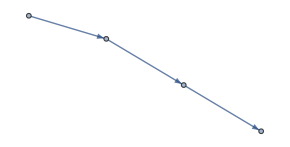

```mathematica
SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2] (* while there are two pegs next to each other, apply IterateTPSMove over the list of peg states*)
```

```mathematica
Graph[SimplePegGameGraph1 (* node arrangement *),
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][
#2 (* node statuses *)],#1(* node poisition *),Center,#3(* node size *)]&), VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->{{1,1,1,1,0}->{4,0},{0,1,1,0,1}->{8,0},{0,0,0,1,1}->{12,0},{1,0,0,0,0}->{16,0}}]
```

-Graphics-

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}

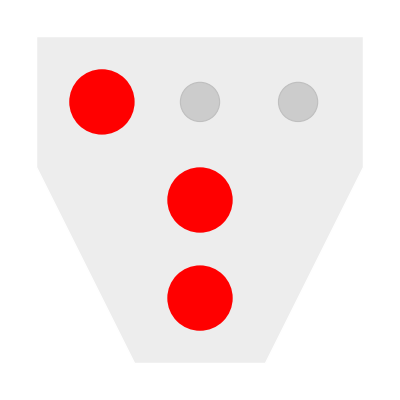

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,1,1,0,0}]
```

```mathematica
With[{indexMapCross=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{4,4}],1]],{{1,1},{1,2},
{1,4},{2,4},{4,4},{4,3},{3,1},{4,1}}]]]},With[{SimplePegGameGraph2={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}],
{ReplacePart[Table[1,{8}],({1,3}/.indexMapCross)->0]},
UnsameQ@@#&,2]},Graph[SimplePegGameGraph2,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapCross][
#2],#1,Center,#3]&),
VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]]]
```

-Graphics-

```mathematica
AbsoluteOptions[%,VertexCoordinates]
```

{VertexCoordinates→{{0.,3.},{0.,2.5},{0.,2.},{-1.,1.5},{0.,1.5},{-1.,1.},{0.,1.},{-1.,0.5},{-1.,0.}}}

```mathematica
indexMapCross
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,2}→5,{3,3}→6,{3,4}→7,{4,2}→8}

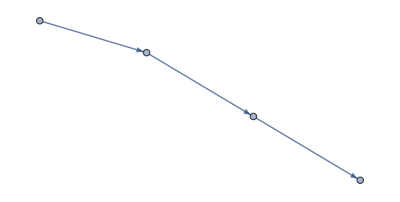

```mathematica
SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2]
```

```mathematica
indexMapCross=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{4,4}],1]],{{1,1},{1,2},
{1,4},{2,4},{4,4},{4,3},{3,1},{4,1}}]]]
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,2}→5,{3,3}→6,{3,4}→7,{4,2}→8}

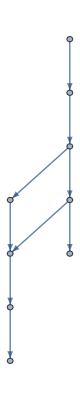

```mathematica
SimplePegGameGraph2={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}, {5,6,8}}],
{ReplacePart[Table[1,{8}],({1,3}/.{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,2}->5,{3,3}->6,{3,4}->7,{4,2}->8})->0]},
UnsameQ@@#&,2]
```

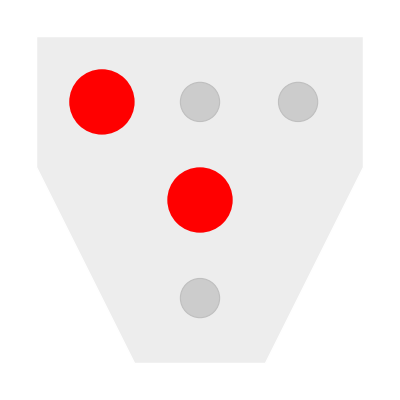

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,0,1,0,0}]
```

```mathematica
(* generates node layout based on all valid moves and starting peg values*)
graphgen[start_,moves_ ]:={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

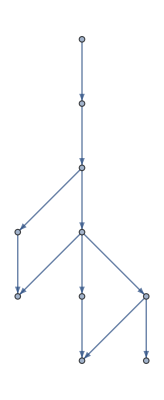

```mathematica
graphgen[{1,1,0,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

```mathematica
visstartingboards[coords_]:=Table[{{"[◼]", "PegSolitaireGraphics"}}[coords][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

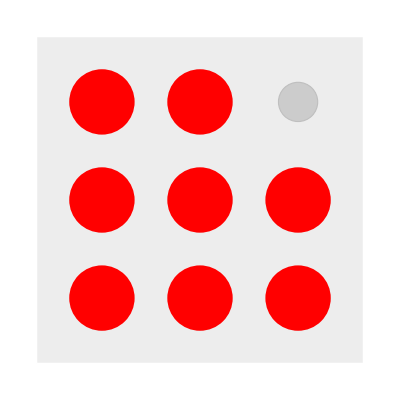
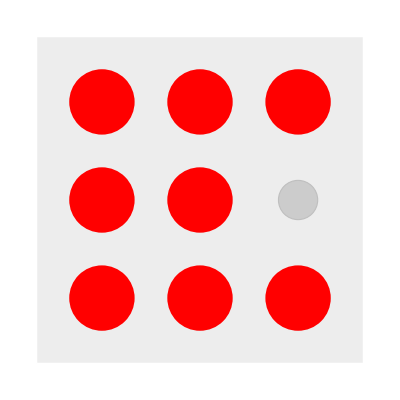
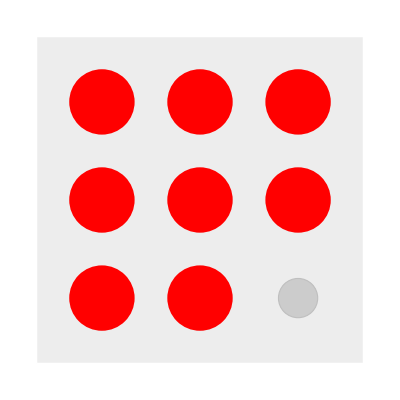
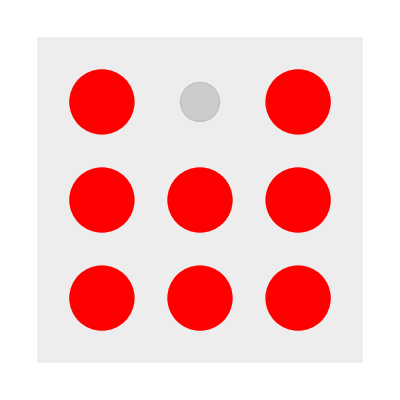
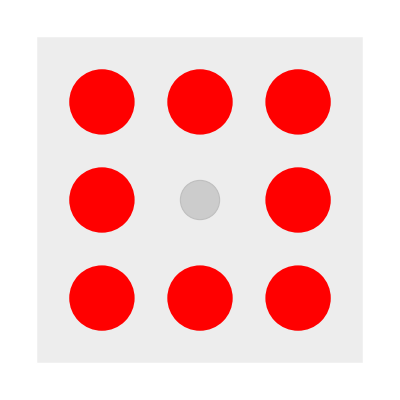
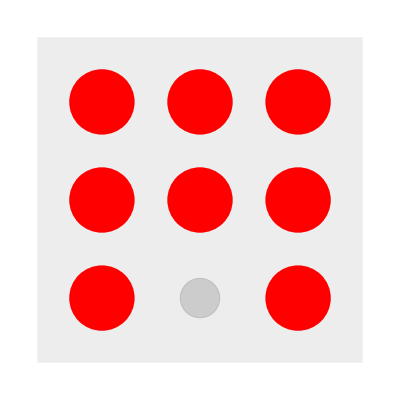
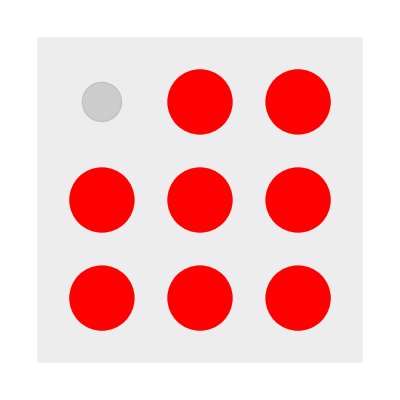
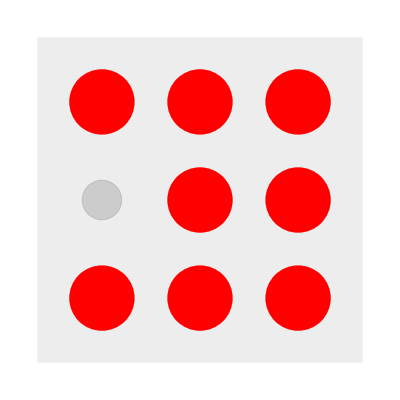

```mathematica
states = visstartingboards[{{1,1}->1,{1,2}->2,{1,3}->3,{2,1}->4,{2,2}->5,{2,3}->6,{3,1}->7,{3,2}->8,{3,3}->9}]
```

```mathematica
newstates = {}
```

{}

```mathematica
For[i=1,i<=Length[states],i++, 
For[j=90,j<=270,j=j+90, 
For[k=i+1, k<=Length[states]-(i+1),k++,
If[ImageRotate[states[[i]],j]===states[[k]], newstates = Delete[states, k]]
]
]
]
```

```mathematica
newstates
```

{}

```mathematica
states
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{}

```mathematica
(*Go through each image in the list of states and check it against each of the other images in the list and check if the color diff has only one dom color (if so then the images are different)*)
For[i=1, i<=Length[states]-1, i++,
For[j=90, j<=270, j=j+90,
For[k=i+1, k<=Length[states], k++,
If[Length[DominantColors[ImageDifference[ImageRotate[states[[i]], j], states[[k]]]]]==1,Append[dupes, states[[k]]]]
]
]
]
```

```mathematica
dupes
```

{}

```mathematica
ImageResize[ImageRotate[-Graphics-],100]
```

-Graphics-

```mathematica
ImageResize[-Graphics-,100]
```

-Graphics-

```mathematica
ImageResize[ImageRotate[-Graphics-],100]===ImageResize[-Graphics-,100]
```

False

```mathematica
ImageDifference[ImageResize[ImageRotate[-Graphics-],100], ImageResize[-Graphics-,100]]
```

-Graphics-

```mathematica
DominantColors[ImageDifference[ImageRotate[-Graphics-], -Graphics-]]
```

{RGBColor[0.00010189464294553333, 0.0001024811068795915, 0.00010248110427860364]}

```mathematica
DominantColors[ImageDifference[ImageResize[ImageRotate[-Graphics-],100], ImageResize[-Graphics-,100]]]
```

```mathematica
ImageDifference[-Graphics-, -Graphics-]
```

-Graphics-

```mathematica
(* If the images are different, the dominate colors of the img difference will not just be black*)
DominantColors[ImageDifference[-Graphics-, -Graphics-]]
```

{RGBColor[0., 2.3370704979557867*^-7, 2.337065217887493*^-7],RGBColor[0.07069081985960773, 0.9292451881270007, 0.9292453343242042]}

```mathematica
multiwaygraph[coords_, start_, moves_] := Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]
```

```mathematica
coords = {{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,2}->5,{3,3}->6,{3,4}->7,{4,2}->8};
start = {1,0,1,1,1,1,1,1};
moves = {{1,4,6},{7,6,5},
{3,5,8},{4,3,2}};
```

```mathematica
multiwaygraph[coords,start,moves]
```

-Graphics-

```mathematica
multiwaygraph[coords,{1,1,1,0,0,0,0,0},moves]
```

-Graphics-

```mathematica
multiwaygraph[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10, {-4,4}->11, {-2,4}->12,{0,4}->13,{2,4}->14, {4,4}->15},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{{1,3,6},{1,2,4},{2,4,7},{2,5,9},{3,5,8},{3,6,10},{4,7,11},{4,8,13},{5,8,12},{5,9,14},{6,9,13},{6,10,15},{4,5,6},{7,8,9},{8,9,10},{11,12,13},{12,13,14},{13,14,15}}]
```

```mathematica
multiwaygraph[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6},{1,1,1,1,1,0},{{1,3,6},{1,2,4},{4,5,6}}]
```

-Graphics-

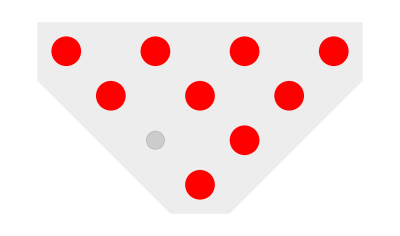
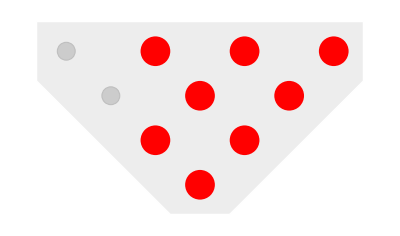
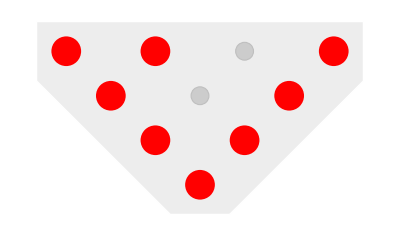
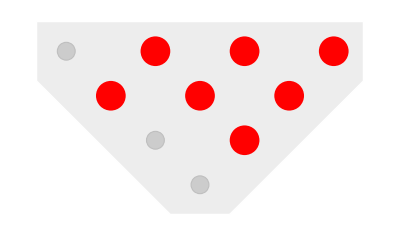
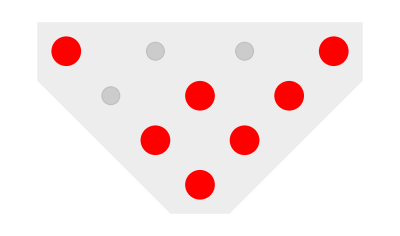
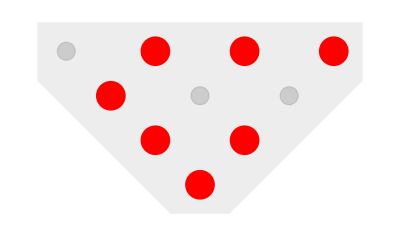
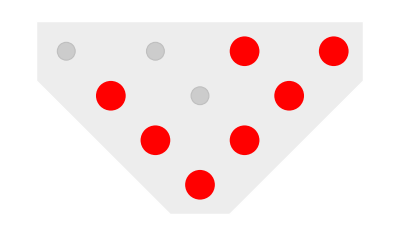
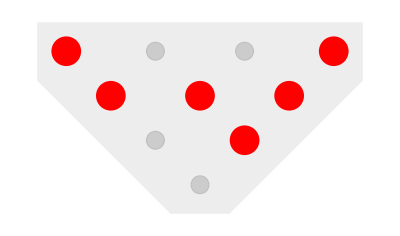

```mathematica
multiwaygraph[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10},{1,0,1,1,1,1,1,1,1,1},{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{3,5,8},{4,5,6},{7,8,9},{8,9,10}}]
```

#### PegSolitaireGraphics

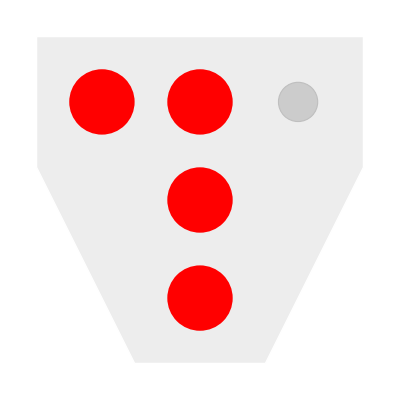

```mathematica
coords = {{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5};
states = {1,1,1,1,0};
{{"[◼]", "PegSolitaireGraphics"}}[coords][states]
```

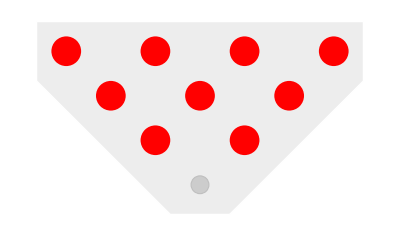

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}][{0,1,1,1,1,1,1,1,1,1}]
```

```mathematica
{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{3,5,8},{4,5,6},{7,8,9},{8,9,10}}
```

{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{3,5,8},{4,5,6},{7,8,9},{8,9,10}}

```mathematica
Append[Table[1, Length[coords]-1],0]
```

{1,1,1,1,0}

```mathematica
visstartingboards[coords_]:=Table[{{"[◼]", "PegSolitaireGraphics"}}[coords][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

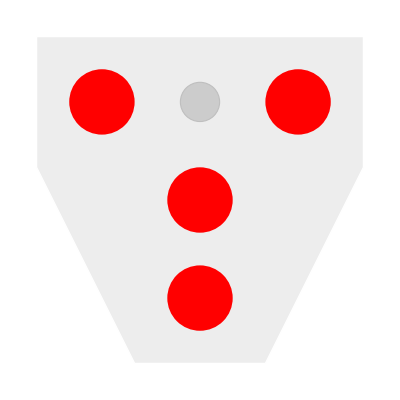
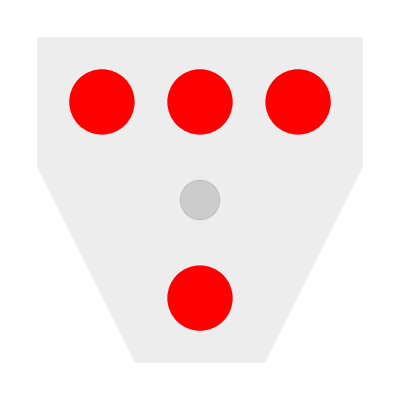
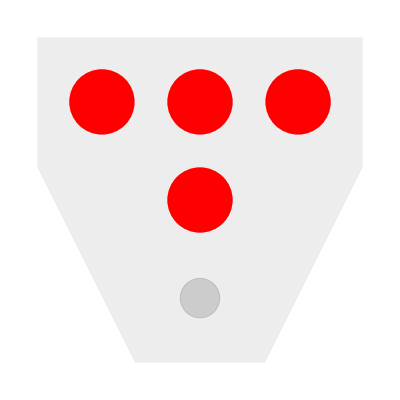
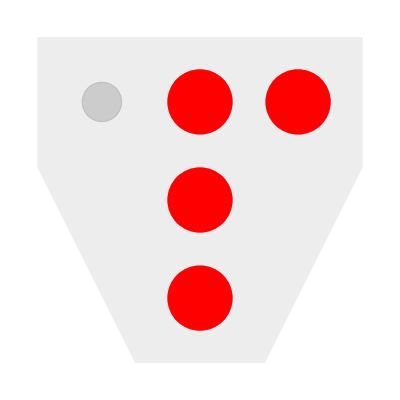
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visstartingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}]
```

```mathematica
visstartingboards[{{1,1}->1,{1,2}->2,{1,3}->3,{2,1}->4,{2,2}->5,{2,3}->6,{3,1}->7,{3,2}->8,{3,3}->9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

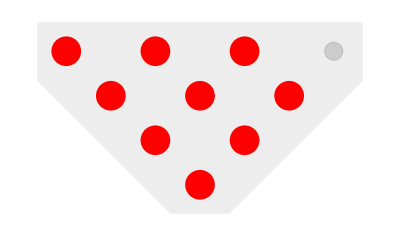
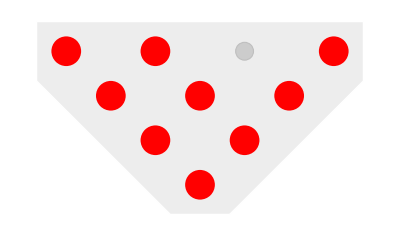
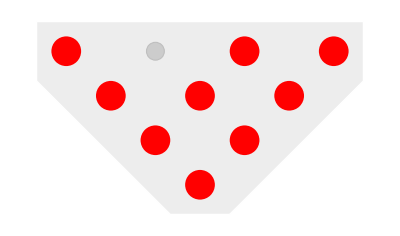
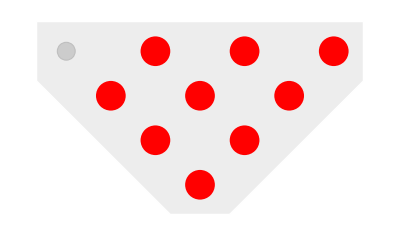
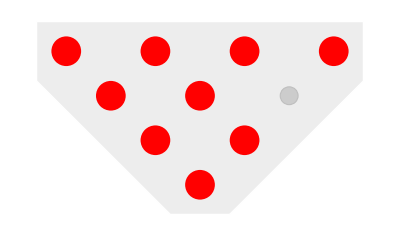
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visstartingboards[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}]
```

```mathematica
visstartingboards[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
startingboards[coords_]:=Permutations[Append[Table[1, Length[coords]-1],0]]
```

```mathematica
startingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}]
```

{{1,1,1,1,0},{1,1,1,0,1},{1,1,0,1,1},{1,0,1,1,1},{0,1,1,1,1}}

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,0,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&
```

Inset[[◼] | PegSolitaireGraphics [indexMapT][#2],#1,Center,#3]&

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,1,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
VertexList@SimplePegGameGraph1
```

{{1,1,1,1,0},{0,1,1,0,1},{0,0,0,1,1},{1,0,0,0,0}}

```mathematica
SimplePegGameGraph1
```

-Graphics-

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}

#### Resource Object stuffs

```mathematica
ResourceFunction["NestWhileGraph"]
```

```mathematica
ResourceFunction["IterateTPSMove"]
```

ResourceObject::notfname: The ResourceObject IterateTPSMove could not be found.

$Failed

```mathematica
ResourceFunction["PegSolitaireGraphics"]
```

ResourceObject::notfname: The ResourceObject PegSolitaireGraphics could not be found.

$Failed

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}
```

[◼] | PegSolitaireGraphics

```mathematica
ResourceObject["PegSolitaireGraphics"]
```

ResourceObject::notfname: The ResourceObject PegSolitaireGraphics could not be found.

$Failed

```mathematica
ResourceSearch["PegSolitaireGraphics"]
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/MultiwayGames/PegSolitaireGraphics/"]
```

[◼] | PegSolitaireGraphics

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/MultiwayGames/IterateTPSMove/"]
```

[◼] | IterateTPSMove

$Aborted